## Setup

### PDE solver

```mathematica
ClearAll@runPARSim2DrotSymm;
Options[runPARSim2DrotSymm]=Join[Options[NDSolve],{"GridPoints"->200}];
runPARSim2DrotSymm[f_,params_,{caInit_,cbInit_,maInit_,mbInit_},tMax_,opts:OptionsPattern[]]:=First@NDSolve[{
D[ca[x,t],t]==Dc/x D[x D[ca[x,t],{x,1}],{x,1}]
+(f[[1]]/.{ca->ca[x,t],cb->cb[x,t],ma->ma[x,t],mb->mb[x,t]}),
D[cb[x,t],t]==Dc /x D[x D[cb[x,t],{x,1}],{x,1}]
+(f[[2]]/.{ca->ca[x,t],cb->cb[x,t],ma->ma[x,t],mb->mb[x,t]}),
D[ma[x,t],t]==Da/x D[x D[ma[x,t],{x,1}],{x,1}]
+(f[[3]]/.{ca->ca[x,t],cb->cb[x,t],ma->ma[x,t],mb->mb[x,t]}),
D[mb[x,t],t]==Db/x D[x D[mb[x,t],{x,1}],{x,1}]
+(f[[4]]/.{ca->ca[x,t],cb->cb[x,t],ma->ma[x,t],mb->mb[x,t]}),
{(* no-flux BCs *)
(D[ca[x,t],x]/.x->0)==0,(D[ca[x,t],x]/.x->L)==0,
(D[cb[x,t],x]/.x->0)==0,(D[cb[x,t],x]/.x->L)==0,
(D[ma[x,t],x]/.x->0)==0,(D[ma[x,t],x]/.x->L)==0,
(D[mb[x,t],x]/.x->0)==0,(D[mb[x,t],x]/.x->L)==0
},
(* initial condition *)
ca[x,0]==caInit[x],
cb[x,0]==cbInit[x],
ma[x,0]==maInit[x],
mb[x,0]==mbInit[x]
}/.params,
{ca,cb,ma,mb},
{x,0,L/.params},
{t,0,tMax},
Evaluate[Sequence@@FilterRules[List@opts,Options[NDSolve]]],Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->OptionValue["GridPoints"],"MaxPoints"->OptionValue["GridPoints"],AccuracyGoal->0,PrecisionGoal->0,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->1},"Method"->{"IDA","ImplicitSolver"->"Newton"}}
];
```

### Finite difference equations for stationary state

```mathematica
discreteGradient[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,1,2]/(2dx)
]
discreteLaplace[data_,dx_]:=With[{paddedData=Join[{data[[1]]},data,{data[[-1]]}]},
Differences[paddedData,2,1]/(dx^2)
]
```

```mathematica
ClearAll@setupFiniteDifferenceEqs;
setupFiniteDifferenceEqs[fA_,fB_,gridRes_]:=With[{
rhoaVec=Thread[rhoa@Range[gridRes]],
rhobVec=Thread[rhob@Range[gridRes]]
},
<|
"UnitGrid"->Range[0.5/gridRes,1,1./gridRes],
"rhoaVec"->rhoaVec,
"rhobVec"->rhobVec,
"Vars"->Join[rhoaVec,{etaa},rhobVec,{etab}],
"Eqs"->{
Da discreteLaplace[rhoaVec,L/gridRes]+(1-Da/Dc)(fA/.{ρa->rhoaVec,ηa->etaa,ρb->rhobVec,ηp->etab}),
rhobarA*gridRes-Total@rhoaVec,
Db discreteLaplace[rhobVec,L/gridRes]+(1-Db/Dc)(fB/.{ρa->rhoaVec,ηa->etaa,ρb->rhobVec,ηb->etab}),
rhobarB*gridRes-Total@rhobVec
}
|>
];
```

```mathematica
getInitGuess[fdSetup_,params_,initSol_]:=Join[
Transpose[{
fdSetup["rhoaVec"],
ma[x,T]+ca[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{etaa,ca[x,T]+Da/Dc*ma[x,T]/.params/.initSol/.x->(L/2/.params)}},
Transpose[{
fdSetup["rhobVec"],
mb[x,T]+cb[x,T]/.params/.initSol/.x->(L/.params) fdSetup["UnitGrid"]
}],
{{etab,cb[x,T]+Db/Dc*mb[x,T]/.params/.initSol/.x->(L/2/.params)}}
]
```

### Finite difference equations for stationary state 2D rot. symm.

```mathematica
ClearAll@setupFiniteDifferenceEqs2DrotSymm;
setupFiniteDifferenceEqs2DrotSymm[fA_,fB_,gridRes_]:=With[{
rhoaVec=Thread[rhoa@Range[gridRes]],
rhobVec=Thread[rhob@Range[gridRes]],
unitGrid=Range[0.5/gridRes,1,1./gridRes]
},
<|
"UnitGrid"->unitGrid,
"rhoaVec"->rhoaVec,
"rhobVec"->rhobVec,
"Vars"->Join[rhoaVec,{etaa},rhobVec,{etab}],
"Eqs"->{
Da(discreteGradient[rhoaVec,L/gridRes]/(L unitGrid)+ discreteLaplace[rhoaVec,L/gridRes])+(1-Da/Dc)(fA/.{ρa->rhoaVec,ηa->etaa,ρb->rhobVec,ηb->etab}),
rhobarA*gridRes/2- Total[unitGrid*rhoaVec],
Db (discreteGradient[rhobVec,L/gridRes]/(L unitGrid)+ discreteLaplace[rhobVec,L/gridRes])+(1-Db/Dc)(fB/.{ρa->rhoaVec,ηa->etaa,ρb->rhobVec,ηb->etab}),
rhobarB*gridRes/2-Total[unitGrid*rhobVec]
}
|>
];
```

### Model setup

PAR reaction kinetics

```mathematica
fa=α ca-(1+k mb^2)ma;
fb=α cb-(1+k ma^2)mb;
```

```mathematica
fA=fa/.{ma->(ρa-ηa)/(1-Da/Dc),ca->(ηa-Da/Dc ρa)/(1-Da/Dc),mb->(ρb-ηb)/(1-Db/Dc),cb->(ηb-Db/Dc ρb)/(1-Db/Dc)};
fB=fb/.{ma->(ρa-ηa)/(1-Da/Dc),ca->(ηa-Da/Dc ρa)/(1-Da/Dc),mb->(ρb-ηb)/(1-Db/Dc),cb->(ηb-Db/Dc ρb)/(1-Db/Dc)};
```

```mathematica
fixedParams={
Da->0.01,Db->0.01,Dc->1000,α-> 1,k-> 60,L->10,T->50000
};
```

```mathematica
fdSetup2DrotSymm=setupFiniteDifferenceEqs2DrotSymm[fA,fB,400];
```

### Setup 2D

```mathematica
run2D=Quiet@runPARSim2DrotSymm[
{-fa,-fb,fa,fb},
Join[{rhobarA->2,rhobarB->2},fixedParams],
{
0&,
0&,
rhobarA*(1+0.5 (Cos[Pi#/L]+(2 L^2)/π^2/(L^2/2)))&,
rhobarB*(1-0.5 (Cos[Pi#/L]+(2 L^2)/π^2/(L^2/2)))&
},
T/.fixedParams,
"GridPoints"->1000
];
```

Initial condition gives average densities rhobarA, rhobarB

```mathematica
Integrate[x Cos[Pi x/L],{x,0,L}]
```

-(2 L^2)/π^2

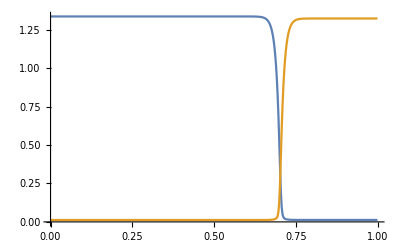

```mathematica
ListLinePlot[
{
Transpose[{x,ma[L x,T/.fixedParams]/.fixedParams/.run2D}/.x->fdSetup2DrotSymm["UnitGrid"]],
Transpose[{x,mb[L x,T/.fixedParams]/.fixedParams/.run2D}/.x->fdSetup2DrotSymm["UnitGrid"]]
},PlotRange->All]
```

Use PDE solution as initial condition to find exact stationary pattern,  i.e., the zero of the finite difference equations

```mathematica
sol2D=Block[{n,eta},FindRoot[
fdSetup2DrotSymm["Eqs"]/.Join[{rhobarA->2,rhobarB->2},fixedParams],
getInitGuess[fdSetup2DrotSymm,fixedParams,run2D],
MaxIterations->100
]
];
```

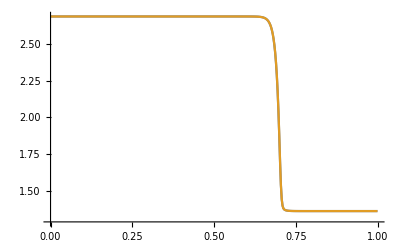

```mathematica
ListLinePlot[{
Transpose[{x,ma[L x,T]+ca[L x,T]/.fixedParams/.run2D}/.x->fdSetup2DrotSymm["UnitGrid"]],
Transpose[{fdSetup2DrotSymm["UnitGrid"],fdSetup2DrotSymm["rhoaVec"]/.sol2D}]
},PlotRange->All]
```

### Continuation 2D, sweeping radius by varying average densities

Load continuation code from separate setup file.
Continuation code programmed by Fridtjof Brauns, published with Brauns et al., PRL 126, 104101 (2021).

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"continuation-setup.nb",
InsertResults->False
];
```

Continuation decreasing domain radius

```mathematica
contData2D=arclengthContinuation[
Flatten@fdSetup2DrotSymm["Eqs"]/.rhobarA->(rhobar-drho)/.rhobarB->(rhobar+drho), (* stat state equations *)
Join[{drho->0,rhobar->2},fixedParams], (* initial parameters *)
sol2D, (* init solution *)
drho, (* continuation parameter *)
10^-2,(* init step size in the arclength parameter s *)
"ParamDomain"->{-0.1,2},
"MaxSteps"->10000,"MaxStepSize"->1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->False
];//AbsoluteTiming
```

{668.184,Null}

Continuation increasing domain radius

```mathematica
contData2D2=arclengthContinuation[
Flatten@fdSetup2DrotSymm["Eqs"]/.rhobarA->(rhobar-drho)/.rhobarB->(rhobar+drho), (* stat state equations *)
Join[{drho->0,rhobar->2},fixedParams], (* initial parameters *)
sol2D, (* init solution *)
drho, (* continuation parameter *)
-10^-2,(* init step size in the arclength parameter s *)
"ParamDomain"->{0.1,-2},
"MaxSteps"->10000,"MaxStepSize"->1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->False
];//AbsoluteTiming
```

{330.695,Null}

Pattern profiles along continuation branch

```mathematica
Manipulate[
ListLinePlot[
{
contData2D["CurveData"][[Floor@i,1,;;400]],
contData2D["CurveData"][[Floor@i,1,402;;801]]
},
PlotRange->{0,3}],
{i,1,Length@contData2D["CurveData"]}]
```

Difference in the mass-redistribution potentials as interface curvature (domain radius) is varied

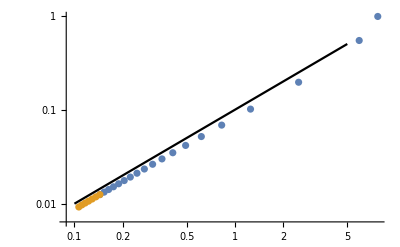

```mathematica
Show[
ListLogLogPlot[{
{1/((L/.fixedParams)Sqrt[(2-#[[-1]]-Min[#[[;;400]]])/(Max[#[[;;400]]]-Min[#[[;;400]]])]),#[[401]]-#[[802]]}&/@contData2D["CurveData"][[;;;;60,1]],
{1/((L/.fixedParams)Sqrt[(2-#[[-1]]-Min[#[[;;400]]])/(Max[#[[;;400]]]-Min[#[[;;400]]])]),#[[401]]-#[[802]]}&/@contData2D2["CurveData"][[;;;;60,1]]
},
PlotRange->All,Joined->False],
LogLogPlot[0.1r,{r,0.1,5},PlotStyle->Black]
]
```

```mathematica
{1/((L/.fixedParams)Sqrt[(2-#[[-1]]-Min[#[[;;400]]])/(Max[#[[;;400]]]-Min[#[[;;400]]])]),#[[401]]-#[[802]]}&/@contData2D["CurveData"][[;;2,1]]
```

{{0.144048,0.0124932},{0.144189,0.0125133}}

### Sweep membrane diffusion coefficients

Continuation increasing membrane diffusion coefficient Da

```mathematica
contData2DDm=arclengthContinuation[
Flatten@fdSetup2DrotSymm["Eqs"]/.rhobarA->(rhobar-drho)/.rhobarB->(rhobar+drho), (* stat state equations *)
Join[{drho->0,rhobar->2},fixedParams], (* initial parameters *)
sol2D, (* init solution *)
Da, (* continuation parameter *)
10^-3,(* init step size in the arclength parameter s *)
"ParamDomain"->{0.001,0.5},
"MaxSteps"->2000,"MaxStepSize"->10^-1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->False
];//AbsoluteTiming
```

{39.0423,Null}

Pattern profiles along continuation branch varying membrane diffusion coefficient Da

```mathematica
Manipulate[
ListLinePlot[
{
contData2DDm["CurveData"][[Floor@i,1,;;400]],
contData2DDm["CurveData"][[Floor@i,1,402;;801]]
},
PlotRange->{0,3}],
{i,1,Length@contData2DDm["CurveData"]}]
```

Continuation increasing both membrane diffusion coefficients Da & Db

```mathematica
contData2DDmDm=arclengthContinuation[
Flatten@fdSetup2DrotSymm["Eqs"]/.Da->Dm/.Db->Dm/.rhobarA->(rhobar-drho)/.rhobarB->(rhobar+drho), (* stat state equations *)
Join[{drho->0,rhobar->2,Dm->Da/.fixedParams},fixedParams], (* initial parameters *)
sol2D, (* init solution *)
Dm, (* continuation parameter *)
10^-3,(* init step size in the arclength parameter s *)
"ParamDomain"->{0.001,0.5},
"MaxSteps"->2000,"MaxStepSize"->10^-1,
"TangentAlignmentThreshold"->0.99,
"TerminateAtFold"->False
];//AbsoluteTiming
```

{34.7856,Null}

Pattern profiles along continuation branch varying membrane diffusion coefficients Da & Db

```mathematica
Manipulate[
ListLinePlot[
{
contData2DDmDm["CurveData"][[Floor@i,1,;;400]],
contData2DDmDm["CurveData"][[Floor@i,1,402;;801]]
},
PlotRange->{0,3}],
{i,1,Length@contData2DDmDm["CurveData"]}]
```

Difference in the mass-redistribution potentials as Da & Db are varied

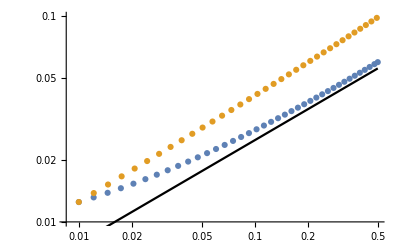

```mathematica
Show[ListLogLogPlot[{
{#[[-1]],(#[[401]]-#[[802]])}&/@contData2DDm["CurveData"][[;;;;2,1]],
{#[[-1]],(#[[401]]-#[[802]])}&/@contData2DDmDm["CurveData"][[;;;;2,1]]
},
PlotRange->{Automatic,{0.01,0.1}},Joined->False],
LogLogPlot[{0.079Sqrt[d]},{d,0.01,0.5},PlotStyle->Black]
]
```